```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\Growth\\Mathematica\\"]
(*********************************************)
```

Preparing

E:\Nutshare\Store\Projects\Growth\Mathematica

The relation between growth and growth index is

Parameters are chosen like this:

```mathematica
Ωd0=0.73
 Ωr0 =8.09*10^-5
H0=71
spli=300000
```

0.73

0.0000809

71

300000

```mathematica
gamma[z_] = Log[f[z]]/Log[Ωm[z]];
```

```mathematica
Ωm[z_]=Ωm0 (1+z)^3
```

(1+z)^3 Ωm0

```mathematica
eE[z_]=√(Ωr0 (1+z)^4+Ωm0 (1+z)^3+Ωd0)
```

√(0.73+0.0000809 (1+z)^4+(1+z)^3 Ωm0)

```mathematica
Hubble[z_]=H0 eE[z]
```

H0 √(0.73+0.0000809 (1+z)^4+(1+z)^3 Ωm0)

```mathematica
Ωmbar[z_]=Ωm[z]/eE[z]^2
```

((1+z)^3 Ωm0)/(0.73+0.0000809 (1+z)^4+(1+z)^3 Ωm0)

## Growth Data

```mathematica
data={{0.15,0.49,0.14},{0.35,0.70,0.18},{0.55,0.75,0.18},{0.77,0.91,0.36},{1.4,0.9,0.24},{2.42,0.74,0.24},{3.00,1.46,0.29},{0.067,0.58,0.11},{0.22,0.6,0.1},{0.41,0.70,0.07},{0.6,0.73,0.07},{0.78,0.70,0.08}}
```

{{0.15,0.49,0.14},{0.35,0.7,0.18},{0.55,0.75,0.18},{0.77,0.91,0.36},{1.4,0.9,0.24},{2.42,0.74,0.24},{3.,1.46,0.29},{0.067,0.58,0.11},{0.22,0.6,0.1},{0.41,0.7,0.07},{0.6,0.73,0.07},{0.78,0.7,0.08}}

```mathematica
len=Length[data]
```

12

```mathematica
data[[5]][[2]]
```

0.9

```mathematica
chi2[γ_,Ωm0_]=Sum[((data[[i]][[2]]-(Ωmbar[data[[i]][[1]]])^γ)/(data[[i]][[3]]))^2,{i,1,len}]
```

82.6446 (0.58-1.21477^γ (Ωm0/(0.730105+1.21477 Ωm0))^γ)^2+51.0204 (0.49-1.52087^γ (Ωm0/(0.730141+1.52087 Ωm0))^γ)^2+100. (0.6-1.81585^γ (Ωm0/(0.730179+1.81585 Ωm0))^γ)^2+30.8642 (0.7-2.46038^γ (Ωm0/(0.730269+2.46038 Ωm0))^γ)^2+204.082 (0.7-2.80322^γ (Ωm0/(0.73032+2.80322 Ωm0))^γ)^2+30.8642 (0.75-3.72388^γ (Ωm0/(0.730467+3.72388 Ωm0))^γ)^2+204.082 (0.73-4.096^γ (Ωm0/(0.73053+4.096 Ωm0))^γ)^2+7.71605 (0.91-5.54523^γ (Ωm0/(0.730794+5.54523 Ωm0))^γ)^2+156.25 (0.7-5.63975^γ (Ωm0/(0.730812+5.63975 Ωm0))^γ)^2+17.3611 (0.9-13.824^γ (Ωm0/(0.732684+13.824 Ωm0))^γ)^2+17.3611 (0.74-40.0017^γ (Ωm0/(0.741068+40.0017 Ωm0))^γ)^2+11.8906 (1.46-64.^γ (Ωm0/(0.75071+64. Ωm0))^γ)^2

```mathematica
chi2[1,0.273]
```

27.6162

Plot::prng: Value of option PlotRange -> {{0.1, 1}, {minimumchi2, 4 + minimumchi2}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

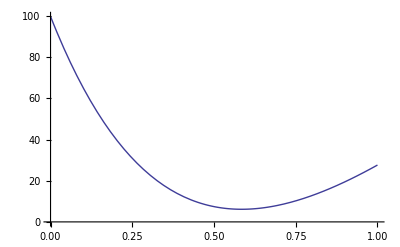

```mathematica
Plot[chi2[γ,0.273],{γ,0,1},PlotRange->{{0.1,1},{minimumchi2,minimumchi2+4}}]
```

```mathematica
minimumchi2=FindMinimum[chi2[x,0.273],{x,0}]
```

{6.13123,{x→0.584558}}

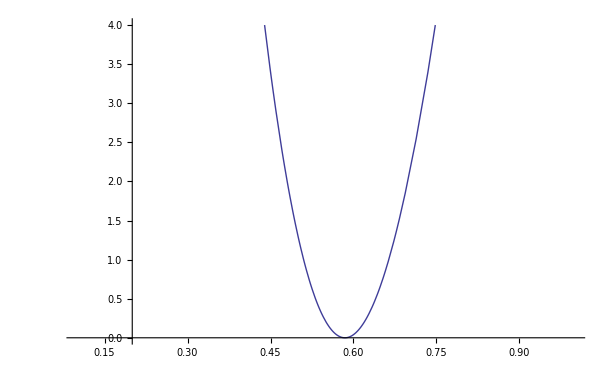

```mathematica
Plot[chi2[γ,0.273]-minimumchi2[[1]],{γ,0,1},PlotRange->{{0.1,1},{0,4}}]
```

```mathematica
Exp[-1/2 chi2[γ,Ωm0]]
```

ⅇ^(1/2 (-82.6446 (0.58-1.21477^γ (Ωm0/(0.730105+1.21477 Ωm0))^γ)^2-51.0204 (0.49-1.52087^γ (Ωm0/(0.730141+1.52087 Ωm0))^γ)^2-100. (0.6-1.81585^γ (Ωm0/(0.730179+1.81585 Ωm0))^γ)^2-30.8642 (0.7-2.46038^γ (Ωm0/(0.730269+2.46038 Ωm0))^γ)^2-204.082 (0.7-2.80322^γ (Ωm0/(0.73032+2.80322 Ωm0))^γ)^2-30.8642 (0.75-3.72388^γ (Ωm0/(0.730467+3.72388 Ωm0))^γ)^2-204.082 (0.73-4.096^γ (Ωm0/(0.73053+4.096 Ωm0))^γ)^2-7.71605 (0.91-5.54523^γ (Ωm0/(0.730794+5.54523 Ωm0))^γ)^2-156.25 (0.7-5.63975^γ (Ωm0/(0.730812+5.63975 Ωm0))^γ)^2-17.3611 (0.9-13.824^γ (Ωm0/(0.732684+13.824 Ωm0))^γ)^2-17.3611 (0.74-40.0017^γ (Ωm0/(0.741068+40.0017 Ωm0))^γ)^2-11.8906 (1.46-64.^γ (Ωm0/(0.75071+64. Ωm0))^γ)^2))

```mathematica
Exp[-1/2 chi2[0.9,1]]
```

0.0000260168

```mathematica
FindMaximum[Exp[-1/2 chi2[γ,Ωm0]],γ,Ωm0]
```

FindMaximum::nrnum: The function value 3.7247×10^-38 - 2.49076×10^-37\ ⅈ is not a real number at {γ, Ωm0} = {0.209916, -0.00060605}.

{0.0485827,{γ→0.483633,Ωm0→0.186466}}

```mathematica
Plot3D[Exp[-1/2(chi2[γ,Ωm0]-minimumchi2[[1]])],{γ,0,1.3},{Ωm0,0.1,0.5}]
```

-Graphics3D-

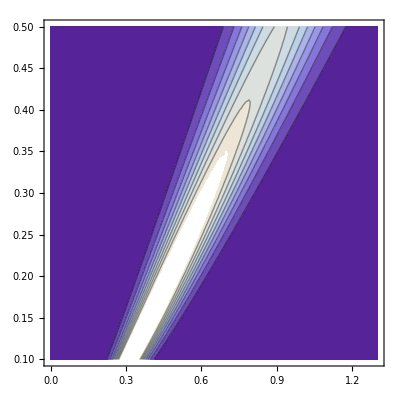

```mathematica
ContourPlot[Exp[-1/2(chi2[γ,Ωm0]-minimumchi2[[1]])],{γ,0,1.3},{Ωm0,0.1,0.5}]
```

## SN Data

At the begining of SCPUnion2_mu_vs_z.txt, a paragraph of words are shown.
#Please cite "Amanullah et al. (The Supernova Cosmology Project), Ap.J., 2010." If the Union2 compilation is included in any other data sets that are distributed,please include this citation request there too.# alpha 0.120887675685
# beta 2.51356117225
# M(h=0.7,statistical only)-19.3111817501
# M(h=0.7,with systematics)-19.3146267582

```mathematica
union2=Import["DATA\\SCPUnion2_mu_vs_z_adjust.txt","Table"];
```

```mathematica
union2[[1,3]]
```

35.3356

```mathematica
lenunion2=Length[union2]
```

557

```mathematica
Clear[snth,minimumchi2union2]
```

```mathematica
snth[z_,Ωm0_]:=5Log[(1+z)NIntegrate[spli/(H0 √(Ωr0 (1+z)^4+Ωm0 (1+z)^3+Ωd0)),{tt,0,z}],10]+25
```

```mathematica
snth[0.5,0.273]
```

26.4741

```mathematica
chi2union2[Ωm0_]:=Sum[((union2[[i]][[3]]-(snth[union2[[i,2]],Ωm0]))/(union2[[i]][[4]]))^2,{i,1,lenunion2}];
```

```mathematica
chi2union2[0.3]
```

3.09173×10^6

```mathematica
minimumchi2union2=FindMinimum[chi2union2[x],x]
```

NIntegrate::inumr: The integrand 300000/71\ √0.730091  + 1.08792\ x
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 0.028488}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

$Aborted

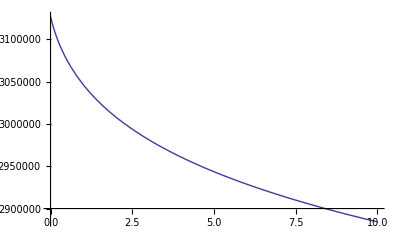

```mathematica
Plot[chi2union2[Ωm0],{Ωm0,0,10}]
```

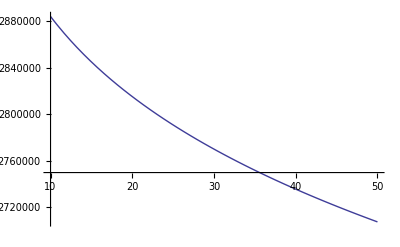

```mathematica
Plot[chi2union2[Ωm0],{Ωm0,10,50}]
```

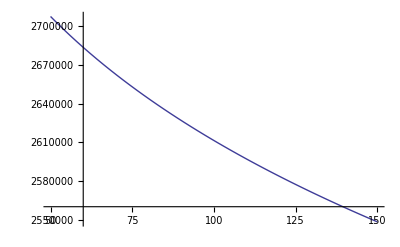

```mathematica
Plot[chi2union2[Ωm0],{Ωm0,50,150}]
```

```mathematica
Plot[chi2union2[γ]-minimumchi2union2[[1]],{γ,0,1}]
```

$Aborted

## United data

```mathematica
chi2union2[Ωm0]+chi2[γ_,Ωm0_]
ContourPlot[Exp[-1/2(chi2[γ,Ωm0]-minimumchi2[[1]])],{γ,0,1.3},{Ωm0,0.1,0.5}]
```

```mathematica
probdis=ProbabilityDistribution[Exp[-1/2 chi2[γ,Ωm0]],{Ωm0,0.1,0.5},{γ,0.1,1.3}]
```

ProbabilityDistribution[ⅇ^(1/2 (-82.6446 (0.58-0.327987^x[2] (1/(0.730105+1.21477 x[1]))^x[2])^2-51.0204 (0.49-0.410636^x[2] (1/(0.730141+1.52087 x[1]))^x[2])^2-100. (0.6-0.490279^x[2] (1/(0.730179+1.81585 x[1]))^x[2])^2-30.8642 (0.7-0.664301^x[2] (1/(0.730269+2.46038 x[1]))^x[2])^2-204.082 (0.7-0.75687^x[2] (1/(0.73032+2.80322 x[1]))^x[2])^2-30.8642 (0.75-1.00545^x[2] (1/(0.730467+3.72388 x[1]))^x[2])^2-204.082 (0.73-1.10592^x[2] (1/(0.73053+4.096 x[1]))^x[2])^2-7.71605 (0.91-1.49721^x[2] (1/(0.730794+5.54523 x[1]))^x[2])^2-156.25 (0.7-1.52273^x[2] (1/(0.730812+5.63975 x[1]))^x[2])^2-17.3611 (0.9-3.73248^x[2] (1/(0.732684+13.824 x[1]))^x[2])^2-17.3611 (0.74-10.8005^x[2] (1/(0.741068+40.0017 x[1]))^x[2])^2-11.8906 (1.46-17.28^x[2] (1/(0.75071+64. x[1]))^x[2])^2)),{x[1],0.1,0.5},{x[2],0.1,1.3}]

```mathematica
datalike=Table[{data[[i,2]],data[[i,1]]},{i,1,Length[data]}]
```

{{0.49,0.15},{0.7,0.35},{0.75,0.55},{0.91,0.77},{0.9,1.4},{0.74,2.42},{1.46,3.},{0.58,0.067},{0.6,0.22},{0.7,0.41},{0.73,0.6},{0.7,0.78}}

```mathematica
Likelihood[probdis,datalike]
```

0

```mathematica
ContourPlot[Log[Likelihood[probdis,data]],{Ωm0,0.1,0.5},{γ,0.1,1.3}]
```

-Graphics-

```mathematica
chi2test[γ_,Ωmbar_,data2_,data3_,length_]=Sum[((data2-(Ωmbar)^γ)/data3)^2,{i,1,length}]
```

(length (data2-Ωmbar^γ)^2)/data3^2

```mathematica
chi2test[γ,Ωmbar[union2[[i,1]]],union2[[i,2]],union2[[i,3]],Length[union2[[i]]]]
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

(2 (-0.27^γ ((«1»)^3/(«1»))^γ+{{1993ah,0.028488,35.3356,0.226144},«555»,{«1»}}⟦i,2⟧)^2)/({{1993ah,0.028488,35.3356,0.226144},«555»,{2001hb,1.03,«14»,0.142161}}⟦«1»⟧)^2